```mathematica
SoftThresh[x_,λ_]:=If[Abs[x]<λ,0,If[x>λ,x-λ,x+λ]]
```

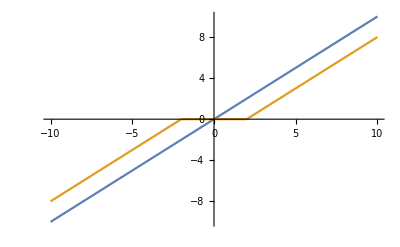

```mathematica
Plot[{x,SoftThresh[x,2]},{x,-10,10}]
```